```mathematica
<<SimpleGroup.m
```

CartanMatrix::shdw: Symbol CartanMatrix appears in multiple contexts {SimpleGroups`,LieART`}; definitions in context SimpleGroups` may shadow or be shadowed by other definitions.

RootSystem::shdw: Symbol RootSystem appears in multiple contexts {SimpleGroups`,LieART`}; definitions in context SimpleGroups` may shadow or be shadowed by other definitions.

DynkinDiagram::shdw: Symbol DynkinDiagram appears in multiple contexts {SimpleGroups`,LieART`}; definitions in context SimpleGroups` may shadow or be shadowed by other definitions.

BuildRep::shdw: Symbol BuildRep appears in multiple contexts {SimpleGroups`,Global`}; definitions in context SimpleGroups` may shadow or be shadowed by other definitions.

DynkinLabels::shdw: Symbol DynkinLabels appears in multiple contexts {SimpleGroups`,Global`}; definitions in context SimpleGroups` may shadow or be shadowed by other definitions.

PlotRep3D::shdw: Symbol PlotRep3D appears in multiple contexts {SimpleGroups`,Global`}; definitions in context SimpleGroups` may shadow or be shadowed by other definitions.

Weight::shdw: Symbol Weight appears in multiple contexts {SimpleGroups`,LieART`}; definitions in context SimpleGroups` may shadow or be shadowed by other definitions.

SimpleRoots::shdw: Symbol SimpleRoots appears in multiple contexts {SimpleGroups`,Global`}; definitions in context SimpleGroups` may shadow or be shadowed by other definitions.

PositiveRoots::shdw: Symbol PositiveRoots appears in multiple contexts {SimpleGroups`,LieART`}; definitions in context SimpleGroups` may shadow or be shadowed by other definitions.

Rank::shdw: Symbol Rank appears in multiple contexts {SimpleGroups`,LieART`}; definitions in context SimpleGroups` may shadow or be shadowed by other definitions.

A::shdw: Symbol A appears in multiple contexts {SimpleGroups`,LieART`}; definitions in context SimpleGroups` may shadow or be shadowed by other definitions.

B::shdw: Symbol B appears in multiple contexts {SimpleGroups`,LieART`}; definitions in context SimpleGroups` may shadow or be shadowed by other definitions.

SU::shdw: Symbol SU appears in multiple contexts {SimpleGroups`,LieART`}; definitions in context SimpleGroups` may shadow or be shadowed by other definitions.

SO::shdw: Symbol SO appears in multiple contexts {SimpleGroups`,LieART`}; definitions in context SimpleGroups` may shadow or be shadowed by other definitions.

OutputMethod::shdw: Symbol OutputMethod appears in multiple contexts {SimpleGroups`,Global`}; definitions in context SimpleGroups` may shadow or be shadowed by other definitions.

MultiplicitiesStyle::shdw: Symbol MultiplicitiesStyle appears in multiple contexts {SimpleGroups`,Global`}; definitions in context SimpleGroups` may shadow or be shadowed by other definitions.

LinksList::shdw: Symbol LinksList appears in multiple contexts {SimpleGroups`,Global`}; definitions in context SimpleGroups` may shadow or be shadowed by other definitions.

Package SimpleGroups (v.0.98β (date:06.05.10)) is loaded

Use SetGroup[] to set the group to work with.

```mathematica
SetGroup[SU[3]]
```

Set group is  A(2)

Rank of the group = 2

```mathematica
Rep1=BuildRep[{1,1}]
```

{{{-1,-1},1},{{1,-2},1},{{0,0},2},{{-2,1},1},{{2,-1},1},{{-1,2},1},{{1,1},1}}

```mathematica
BuildRep[{1,1}]
```

{{{-1,-1},1},{{1,-2},1},{{0,0},2},{{-2,1},1},{{2,-1},1},{{-1,2},1},{{1,1},1}}

```mathematica
rep3=BuildRep[{1,0}]
```

{{{0,-1},1},{{-1,1},1},{{1,0},1}}

```mathematica
rep3bar=BuildRep[{0,1}]
```

{{{-1,0},1},{{1,-1},1},{{0,1},1}}

```mathematica
CGDecomposition[rep3, rep3, rep3];
CGDecomposition[rep3, rep3bar];
```

3 ⊗ 3 ⊗ 3 = 10 ⊕ 8 ⊕ 8 ⊕ 1

3 ⊗ 3 = 8 ⊕ 1

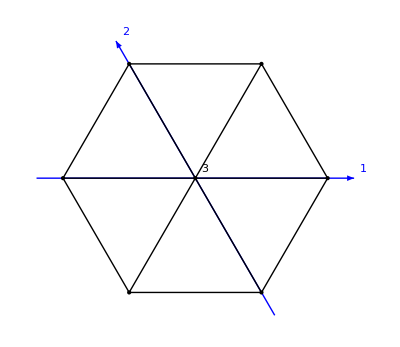

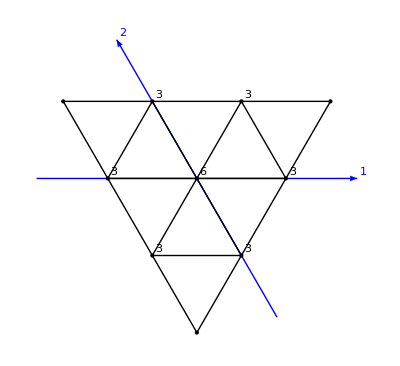

```mathematica
rep3wts=BuildRep[{1,0}, OutputMethod->"Weights"];
rep3barwts=BuildRep[{0,1}, OutputMethod->"Weights"];
repMeson=RepProduct[rep3wts, rep3barwts];
repBaryon=RepProduct[RepProduct[rep3wts, rep3wts], rep3wts];
PlotRep2D[repMeson, SimpleRoots]
PlotRep2D[repBaryon, SimpleRoots]
```

```mathematica
SetGroup[SU[4]]
```

Set group is  A(3)

Rank of the group = 3

```mathematica
BuildRep[{1,1,0},OutputMethod->"Weights"]
```

{{{-3/4,-3/4,1/4,5/4},1},{{-3/4,1/4,-3/4,5/4},1},{{1/4,-3/4,-3/4,5/4},1},{{-3/4,1/4,1/4,1/4},2},{{1/4,-3/4,1/4,1/4},2},{{1/4,1/4,-3/4,1/4},2},{{-3/4,-3/4,5/4,1/4},1},{{-3/4,5/4,-3/4,1/4},1},{{5/4,-3/4,-3/4,1/4},1},{{-3/4,1/4,5/4,-3/4},1},{{1/4,-3/4,5/4,-3/4},1},{{1/4,1/4,1/4,-3/4},2},{{-3/4,5/4,1/4,-3/4},1},{{5/4,-3/4,1/4,-3/4},1},{{1/4,5/4,-3/4,-3/4},1},{{5/4,1/4,-3/4,-3/4},1}}

```mathematica
repSinglet={{{-3/4,-3/4,1/4,5/4},"uus"},{{-3/4,1/4,-3/4,5/4},"uud"},{{1/4,-3/4,-3/4,5/4},"uuc"},{{-3/4,1/4,1/4,1/4},"uds(2)"},{{1/4,-3/4,1/4,1/4},"usc(2)"},{{1/4,1/4,-3/4,1/4},"udc(2)"},{{-3/4,-3/4,5/4,1/4},"uss"},{{-3/4,5/4,-3/4,1/4},"udd"},{{5/4,-3/4,-3/4,1/4},"ucc"},{{-3/4,1/4,5/4,-3/4},"dss"},{{1/4,-3/4,5/4,-3/4},"ssc"},{{1/4,1/4,1/4,-3/4},"dsc(2)"},{{-3/4,5/4,1/4,-3/4},"dds"},{{5/4,-3/4,1/4,-3/4},"scc"},{{1/4,5/4,-3/4,-3/4},"ddc"},{{5/4,1/4,-3/4,-3/4},"dcc"}};
PlotRep3D[repSinglet, SimpleRoots, LinksList->{SimpleRoots[[2]], SimpleRoots[[3]], SimpleRoots[[2]]+SimpleRoots[[3]]},MultiplicitiesStyle->{12}]
```

-Graphics3D-

```mathematica
repSingletNamed={{{-3/4,-3/4,1/4,5/4},"Σ^+"},{{-3/4,1/4,-3/4,5/4},"p"},{{1/4,-3/4,-3/4,5/4},"Σ_c^(++)"},{{-3/4,1/4,1/4,1/4},"Λ, Σ^0"},{{1/4,-3/4,1/4,1/4},"Ξ_c^+"},{{1/4,1/4,-3/4,1/4},"Λ_c^+, Σ_c^+"},{{-3/4,-3/4,5/4,1/4},"Ξ^0"},{{-3/4,5/4,-3/4,1/4},"n"},{{5/4,-3/4,-3/4,1/4},"Ξ_cc^(++)"},{{-3/4,1/4,5/4,-3/4},"Ξ^-"},{{1/4,-3/4,5/4,-3/4},"Ω_c^0"},{{1/4,1/4,1/4,-3/4},"Ξ_c^0"},{{-3/4,5/4,1/4,-3/4},"Σ^-"},{{5/4,-3/4,1/4,-3/4},"Ω_cc^+"},{{1/4,5/4,-3/4,-3/4},"Σ_c^0"},{{5/4,1/4,-3/4,-3/4},"Ξ_cc^+"}};
PlotRep3D[repSingletNamed, SimpleRoots, LinksList->{SimpleRoots[[2]], SimpleRoots[[3]], SimpleRoots[[2]]+SimpleRoots[[3]]},MultiplicitiesStyle->{12}]
```

-Graphics3D-

```mathematica
SimpleRoots
```

{{1,-1,0,0},{0,1,-1,0},{0,0,1,-1}}

```mathematica
BuildRep[{3,0,0},OutputMethod->"Weights"]
```

{{{-3/4,-3/4,-3/4,9/4},1},{{-3/4,-3/4,1/4,5/4},1},{{-3/4,1/4,-3/4,5/4},1},{{1/4,-3/4,-3/4,5/4},1},{{-3/4,-3/4,5/4,1/4},1},{{-3/4,1/4,1/4,1/4},1},{{1/4,-3/4,1/4,1/4},1},{{-3/4,5/4,-3/4,1/4},1},{{1/4,1/4,-3/4,1/4},1},{{5/4,-3/4,-3/4,1/4},1},{{-3/4,-3/4,9/4,-3/4},1},{{-3/4,1/4,5/4,-3/4},1},{{1/4,-3/4,5/4,-3/4},1},{{-3/4,5/4,1/4,-3/4},1},{{1/4,1/4,1/4,-3/4},1},{{5/4,-3/4,1/4,-3/4},1},{{-3/4,9/4,-3/4,-3/4},1},{{1/4,5/4,-3/4,-3/4},1},{{5/4,1/4,-3/4,-3/4},1},{{9/4,-3/4,-3/4,-3/4},1}}

```mathematica
RepTriplet={{{-3/4,-3/4,-3/4,9/4},"sss"},{{-3/4,-3/4,1/4,5/4},"dss"},{{-3/4,1/4,-3/4,5/4},"uss"},{{1/4,-3/4,-3/4,5/4},"ssc"},{{-3/4,-3/4,5/4,1/4},"dds"},{{-3/4,1/4,1/4,1/4},"uds"},{{1/4,-3/4,1/4,1/4},"dsc"},{{-3/4,5/4,-3/4,1/4},"uus"},{{1/4,1/4,-3/4,1/4},"usc"},{{5/4,-3/4,-3/4,1/4},"scc"},{{-3/4,-3/4,9/4,-3/4},"ddd"},{{-3/4,1/4,5/4,-3/4},"udd"},{{1/4,-3/4,5/4,-3/4},"ddc"},{{-3/4,5/4,1/4,-3/4},"uud"},{{1/4,1/4,1/4,-3/4},"udc"},{{5/4,-3/4,1/4,-3/4},"dcc"},{{-3/4,9/4,-3/4,-3/4},"uuu"},{{1/4,5/4,-3/4,-3/4},"uuc"},{{5/4,1/4,-3/4,-3/4},"ucc"},{{9/4,-3/4,-3/4,-3/4},"ccc"}};
PlotRep3D[RepTriplet, SimpleRoots, LinksList->{SimpleRoots[[2]], SimpleRoots[[3]], SimpleRoots[[2]]+SimpleRoots[[3]]},MultiplicitiesStyle->{12}]
```

-Graphics3D-

Now we will put the formal names for each triplet baryon according to the following convention:
1. Baryons with all 1st generation quarks are named Δ. Those with 2 first generation and one second generation quarks are named Σ. Those with 1 from first generation and 2 from second generation are named Ξ, and those with all second generation quarks are named Ω.
2. One or more c’s in the subscript denotes the number of charm quarks present.
3. The superscript denotes the electric charge.

```mathematica
RepTripletNamed={{{-3/4,-3/4,-3/4,9/4},"Ω^-"},{{-3/4,-3/4,1/4,5/4},"Ξ^-"},{{-3/4,1/4,-3/4,5/4},"Ξ^0"},{{1/4,-3/4,-3/4,5/4},"Ω_c^0"},{{-3/4,-3/4,5/4,1/4},"Σ^-"},{{-3/4,1/4,1/4,1/4},"Σ^0"},{{1/4,-3/4,1/4,1/4},"Ξ_c^0"},{{-3/4,5/4,-3/4,1/4},"Σ^+"},{{1/4,1/4,-3/4,1/4},"Ξ_c^+"},{{5/4,-3/4,-3/4,1/4},"Ω_cc^+"},{{-3/4,-3/4,9/4,-3/4},"Δ^-"},{{-3/4,1/4,5/4,-3/4},"Δ^0"},{{1/4,-3/4,5/4,-3/4},"Σ_c^0"},{{-3/4,5/4,1/4,-3/4},"Δ^+"},{{1/4,1/4,1/4,-3/4},"Σ_c^+"},{{5/4,-3/4,1/4,-3/4},"Ξ_cc^+"},{{-3/4,9/4,-3/4,-3/4},"Δ^(++)"},{{1/4,5/4,-3/4,-3/4},"Σ_c^(++)"},{{5/4,1/4,-3/4,-3/4},"Ξ_cc^(++)"},{{9/4,-3/4,-3/4,-3/4},"Ω_ccc^(++)"}};
PlotRep3D[RepTripletNamed, SimpleRoots, LinksList->{SimpleRoots[[2]], SimpleRoots[[3]], SimpleRoots[[2]]+SimpleRoots[[3]]},MultiplicitiesStyle->{12}]
```

-Graphics3D-

```mathematica
BuildRep[{3,0,0},OutputMethod->"Weights"]
```

{{{-3/4,-3/4,-3/4,9/4},1},{{-3/4,-3/4,1/4,5/4},1},{{-3/4,1/4,-3/4,5/4},1},{{1/4,-3/4,-3/4,5/4},1},{{-3/4,-3/4,5/4,1/4},1},{{-3/4,1/4,1/4,1/4},1},{{1/4,-3/4,1/4,1/4},1},{{-3/4,5/4,-3/4,1/4},1},{{1/4,1/4,-3/4,1/4},1},{{5/4,-3/4,-3/4,1/4},1},{{-3/4,-3/4,9/4,-3/4},1},{{-3/4,1/4,5/4,-3/4},1},{{1/4,-3/4,5/4,-3/4},1},{{-3/4,5/4,1/4,-3/4},1},{{1/4,1/4,1/4,-3/4},1},{{5/4,-3/4,1/4,-3/4},1},{{-3/4,9/4,-3/4,-3/4},1},{{1/4,5/4,-3/4,-3/4},1},{{5/4,1/4,-3/4,-3/4},1},{{9/4,-3/4,-3/4,-3/4},1}}